```mathematica
Print[Button[Style["Quit Kernel",Bold],Quit[],ImageSize->{150,35}]]
```

Quit Kernel

Folgendes Integral soll minimiert bzw. maximiert (Vorzeichen des Integrandens wird invertiert) werden:

ℐ=∫_t_1^t_2 F(t,𝓏_1, (𝓏̇)_1,𝓏_2)ⅆt→min , bzw.  ℐ=∫_t_1^t_2 -F(t,𝓏_1, (𝓏̇)_1,𝓏_2)ⅆt→max

In dem Funktionenvektor 𝓏_1 sind alle Funktionen enthalten, deren erste Ableitungen in F(t,𝓏_1, (𝓏̇)_1,𝓏_2) vorkommen.
In dem Funktionenvektor 𝓏_2 hingegen sind alle Funktionen enthalten, deren erste Ableitungen in F(t,𝓏_1, (𝓏̇)_1,𝓏_2) nicht vorkommen. 𝓏_2 ist in der Regel ausschließlich im 3. Fall vorhanden!

2. Fall: Ein weiteres Integral soll einen festen Wert τ annehmen:

τ=∫_t_1^t_2 G(t,𝓏_1, (𝓏̇)_1)ⅆt

Für das resultierende Differentialgleichungssystem gilt:

H(t,𝓏_1, (𝓏̇)_1,λ)=F(t,𝓏_1, (𝓏̇)_1)+λ G(t,𝓏_1, (𝓏̇)_1)
0=∇_𝓏_1 H(t,𝓏_1, (𝓏̇)_1,λ)-ⅆ/ⅆt∇_((𝓏̇)_1) H(t,𝓏_1, (𝓏̇)_1,λ)

## Eingabe (F, 𝓏_1, 𝓏_2, 𝓃ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃, G)

```mathematica
ClearAll["Global`*"]
F[t_]=y1[t]^2+D[y1[t],t]^2+y2[t]^2+D[y2[t],t]^2;
𝓏1[t_]={y1[t],y2[t]};
𝓏2[t_]={};
𝓃ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃={y1[0]==1,y1[2]==0,y2[0]==0,y2[2]==1};
G[t_]=y1[t]+D[y1[t],t]+y2[t]+D[y2[t],t];
```

## Programm (automatisch)

```mathematica
(*Programm*)
<<VariationalMethods`
H[t_]=F[t]+λAllgemein G[t];
𝓏[t_]=Join[𝓏1[t],𝓏2[t]];
𝒹ℊℓ𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽=Table[
FullSimplify[VariationalD[H[t],𝓏[t],t]][[i]]==0,
{i,Length[𝓏[t]]}];

(*Ausgabe*)
Print[StringForm["``",
𝒹ℊℓ𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽//TableForm]]
```

λAllgemein+2 y1[t]-2 y1''[t]==0
λAllgemein+2 y2[t]-2 y2''[t]==0

## Programm (manuell)

```mathematica
(*Programm*)
H[t_]=F[t]+λAllgemein G[t];
𝓏[t_]=Join[𝓏1[t],𝓏2[t]];
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ=Table[
FullSimplify[(Grad[H[t],𝓏[t]]-D[Grad[H[t],𝓏'[t]],t])[[i]]]==0,
{i,Length[𝓏[t]]}];

(*Ausgabe*)
Print[StringForm["``",
𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ//TableForm]]
```

λAllgemein+2 y1[t]-2 y1''[t]==0
λAllgemein+2 y2[t]-2 y2''[t]==0

## Programm (Differentialgleichung)

```mathematica
(*Programm*)
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t_]=Flatten[FullSimplify[N[DSolve[Join[𝒹ℊℓℳ𝒶𝓃𝓊ℯℓℓ,𝓃ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃],𝓏[t],t]]]][[All,2]];

(*Ausgabe*)
Print[StringForm["𝓎_allgemein(t) = ``",
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t]//MatrixForm]]
```

𝓎_allgemein(t) = (0.0596015 (-7.38906+2.71828^t) ⅇ^(-1. t) (-2.31304-0.313035 2.71828^t+(-1.+1. 2.71828^t) λAllgemein)
0.0596015 (-1.+2.71828^t) ⅇ^(-1. t) (2.31304+2.31304 2.71828^t+(-7.38906+1. 2.71828^t) λAllgemein))

## Programm (λ)

𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽 entspricht den Integrationsgrenzen bzw. den Nebenbedingungen:

```mathematica
G=𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t][[1]]+D[𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t][[1]],t]+𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t][[2]]+D[𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t][[2]],t];
τ=3;
𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽={0,2};
```

```mathematica
(*Programm*)
λ=λAllgemein/.Flatten[Solve[τ==Integrate[G,{t,𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[1]],𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[2]]}],λAllgemein]];
𝓎[t_]=FullSimplify[𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t]/.λAllgemein->λ];

(*Ausgabe*)
Print[StringForm["λ = ``\n𝓎(t) = ``",
λ,
𝓎[t]//MatrixForm]]
```

λ = -3.09726
𝓎(t) = (1.54863-0.548632 Cosh[1. t]+0.142114 Sinh[1. t]
1.54863-1.54863 Cosh[1. t]+1.45515 Sinh[1. t])

## Plot

𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽 entspricht den Integrationsgrenzen bzw. den Nebenbedingungen:

```mathematica
𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽={0,2};
```

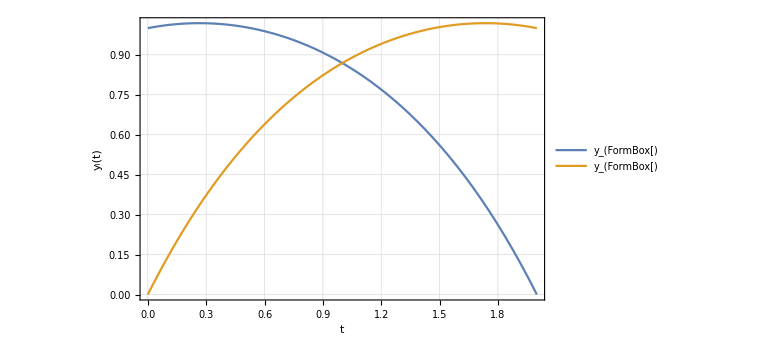

```mathematica
(*Ausgabe*)
plot=Plot[Evaluate[𝓎[t]],{t,𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[1]],𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[2]]},
PlotRange->All,Frame->True,FrameLabel->{"t","y_i(t)"},GridLines->Automatic,
PlotLegends->Table[StringForm["y_(``)",i],{i,Length[𝓎[t]]}],
ImageSize->Large];
Print[Show[plot]]
```